```mathematica
Clear["Global`*"]
```

```mathematica
{FileNameSetter[Dynamic[ff],"OpenList"],Dynamic[ff]}
```

```mathematica
{$CellContext`ffOpenListAll,}
```

{$CellContext`ffOpenListAll,}

0.107143

0.107143

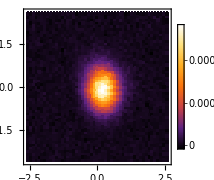
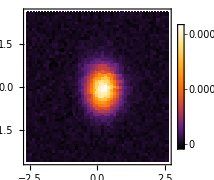
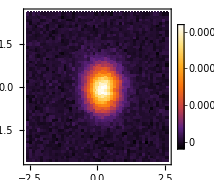
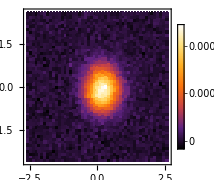
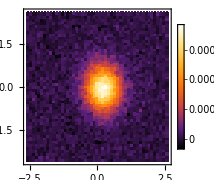
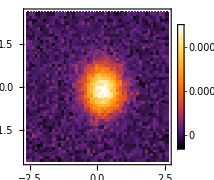

{99,99}

```mathematica
io=2;(*interpolation order*)
negate=-1;(*needs to be changed to -1 if the signal sign is negative*)
timearray ={01,05,10,20,30,50};(*  {0,50,100,250}*)(*{1.,5.,10.,25.,50.,75.,100}*);(*in ps - same number as # of files*)
dat=Import[#,"Table"]&/@ff;
nx =50;(*number of rows pixels*)
ny=50;(*number of cols pixels*)
nangles=16;(*number of angles around 2π to calculate diffusion coefficients*)
xmin = Min[dat[[1,;;,1]]];
xmax=Max[dat[[1,;;,1]]];
ymin=Min[dat[[1,;;,2]]];
ymax=Max[dat[[1,;;,2]]];
dx=(xmax-xmin)/(nx-1)
dy=(ymax-ymin)/(ny-1)
dg[dt_,dc_,x_]:=Quiet[If[dt≠0, Exp[-x^2/(4 dc dt)]/√(4 Pi dc dt),KroneckerDelta[Chop[x,10^-3],0.]]];(*Green's Function def*)
zdat=dat[[;;,;;,3]];
zimage=negate*Table[ArrayReshape[{zdat[[i,;;]]},{nx,ny}],{i,1,Length[ff]}];
Do[zimage[[k,i,;;]]=Reverse[zimage[[k,i,;;]]],{i,2,Length[zimage[[1,;;,1]]],2},{k,1,Length[ff]}];(*NOTICE! NOTICE! NOTICE! uncomment this line for data from the microscope - accounts for serpentine scanning pattern*)
(*pad=.45;
test=Table[ListInterpolation[zimage[[i]],{{xmin,xmax},{ymin,ymax}},InterpolationOrder->0],{i,1,Length[timearray]}];
nzimage=Table[test[[i]][j,k],{i,1,Length[timearray]},{j,xmin-pad,xmax+pad,dx/io},{k,ymin-pad,ymax+pad,dy/io}];
xmin = xmin-pad;
xmax=xmax+pad;
ymin=ymin-pad;
ymax=ymax+pad;*)
nzimage=zimage;
Table[ListDensityPlot[nzimage[[i]],PlotLegends->Automatic,DataRange->{{(xmin-xmax)/2,(xmax-xmin)/2},{(ymin-ymax)/2,(ymax-ymin)/2}},ColorFunction->"SunsetColors",PlotRange->All,ClippingStyle->Black,BaseStyle->{FontName->"Arial"},InterpolationOrder->0,ImageSize->Small],{i,1,Length[ff]}]
f=Table[ListInterpolation[nzimage[[i]],{{xmin,xmax},{ymin,ymax}},InterpolationOrder->2],{i,1,Length[timearray]}];
nzimage2=Table[f[[i]][j,k],{i,1,Length[timearray]},{j,xmin,xmax,dx/io},{k,ymin,ymax,dy/io}];
(*nzimage2=nzimage;*)
{nx2,ny2}=Dimensions[nzimage2[[1]]]
DynamicModule[{p={20,20}},
{LocatorPane[Dynamic[p],Image[Reverse[nzimage2[[1]]]/Max[nzimage2[[1]]],ImageSize->Large]],Dynamic[Floor[p]]}
]
(*DynamicModule[{p={20,20}},
{LocatorPane[Dynamic[p],Image[Reverse[nzimage2[[5]]]/Max[nzimage2[[5]]],ImageSize->Large]],Dynamic[Floor[p]]}
]*)
```

```mathematica
.
```

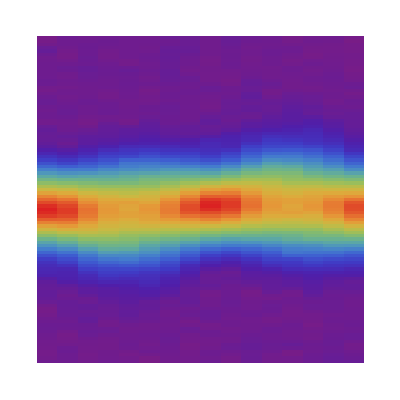
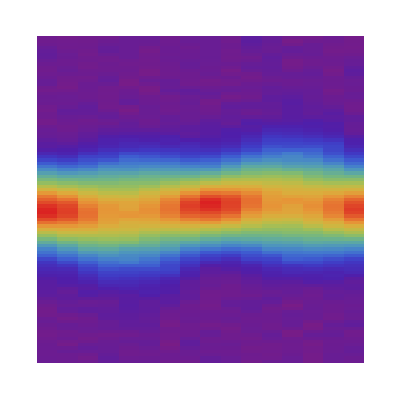
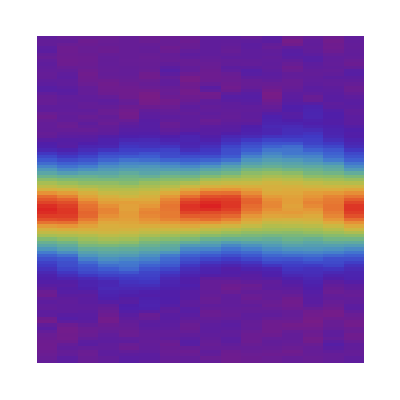
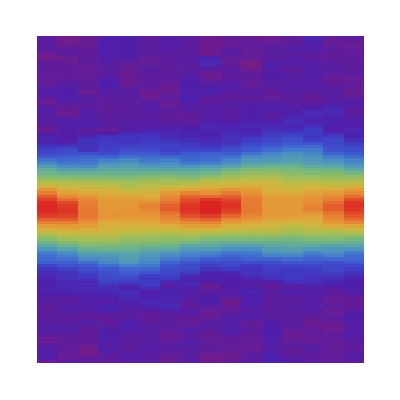
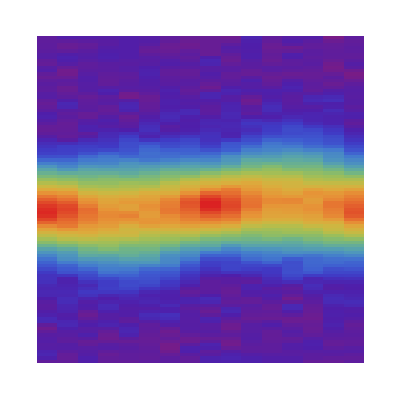
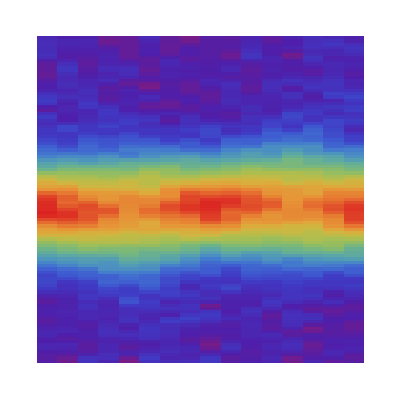

```mathematica
Clear[polardat,polardat2]
colcoord=52;
rowcoord=46;
lcoord=Max[{colcoord,rowcoord}];
polardat=Table[ImageTransformation[Image[Reverse[nzimage2[[i]]]/Max[nzimage2[[i]]]],RotationTransform[k,{colcoord/nx2,rowcoord/ny2}],Padding->"Fixed",Resampling->"Linear"],{k,0,(nangles-1)Pi/(nangles/2),Pi/(nangles/2)},{i,1,Length[ff]}];
polardat2=Table[ImageData[polardat[[k,i]]],{k,1,nangles},{i,1,Length[ff]}];
polardat2=Total[polardat2,{3}];
polardat=Table[polardat2[[i,k,j]](*-Min[polardat2[[i,1,;;]]]*),{k,1,Length[ff]},{j,1,nx2},{i,1,nangles}];
(*polardat=Table[polardat[[k,;;,j]]/Max[polardat[[k,;;,j]]],{k,1,Length[ff]},{j,1,nangles}];*)
Table[ArrayPlot[polardat[[i,;;,;;]],ColorFunction->"Rainbow",AspectRatio->1],{i,1,Length[ff]}]
```

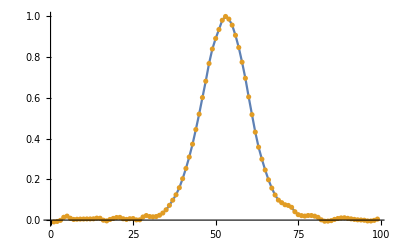

FittedModel::constr: The property values {ParameterTableEntries} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{0,8.05989,0.188877},{π/8,9.33749,0.225486},{π/4,8.5506,0.267039},{(3 π)/8,6.539,0.370056},{π/2,9.82906,0.396794},{(5 π)/8,9.31385,0.362821},{(3 π)/4,8.33752,0.309451},{(7 π)/8,8.96888,0.230733},{π,9.46836,0.280004},{(9 π)/8,11.2784,0.269095},{(5 π)/4,11.3931,0.332645},{(11 π)/8,10.8099,0.419509},{(3 π)/2,10.4614,0.493318},{(13 π)/8,8.42368,0.357906},{(7 π)/4,8.39724,0.277829},{(15 π)/8,7.58694,0.255167}}

```mathematica
Clear[difffit,metafit,nlm2,G1,test1,middle,fitdat,dcvals];
G1=Table[dg[1.,.0001,(x-(xmax-xmin)/2)],{x,0,(xmax-xmin),dx/io}];
Table[(x-(xmax-xmin)/2),{x,0,(xmax-xmin),dx/io}];
middle=If[EvenQ[nx2],nx2/2,(nx2+1)/2];
test1=ListConvolve[G1,polardat[[1,;;,1]],{middle,middle}];
ListPlot[{test1/Max[test1],polardat[[1,;;,1]]/Mean[TakeLargest[polardat[[1,;;,1]],1]]},PlotRange->All,Joined->{True,False}]
fitdat=Table[{timearray[[i]]-timearray[[1]],x,polardat[[i,x,rad]]/Mean[TakeLargest[polardat[[i,;;,rad]],1]]},{i,1,Length[timearray]},{x,1,nx2},{rad,1,Last[Dimensions[polardat,3]]}];
fitdat=Flatten[fitdat,1];
difffit[dt_?NumericQ,dc_?NumericQ,initialprof_]:=difffit[dt,dc,initialprof]=Module[{m1},
m1=ListConvolve[Table[dg[dt,dc,x-(xmax-xmin)/2],{x,0,(xmax-xmin),dx/io}],initialprof,{middle,middle}];
m1/Mean[TakeLargest[m1,1]]
];
metafit[dt_?NumericQ,dc_?NumericQ,x_?NumericQ,initialprof_]:=difffit[dt,dc,initialprof][[x]];
weights=Catenate[Table[Boole[(i>colcoord)],{i,1,nx2,1},{j,1,Length[timearray]}]ᵀ];
nlm2=ParallelTable[Quiet[NonlinearModelFit[fitdat[[;;,radcomp,;;]],{metafit[t,dc,x1,ListConvolve[G1,polardat[[1,;;,radcomp]],{middle,middle}]],dc≥0.},{{dc,.0001}},{t,x1},Weights->weights,ConfidenceLevel->.9]],{radcomp,nangles}];
dcvals=Table[
Catenate[{{(radcomp-1)*2Pi/nangles},10000*First[nlm2[[radcomp]]["ParameterTableEntries"]][[1;;2]]}],
{radcomp,nangles}]
```

```mathematica
(*SaveDestination="/Users/erikgrumstrup/OneDrive - Montana State University - Bozeman/_Workspace/Papers Local/2019-2020/Green's Function Diffusion/test data/figure 1 files/";
Export[SaveDestination<>"1wrongperfectgaussNCDs",Table[{(i-1) Pi/(nangles/2),10000*nlm2[[i]]["ParameterTableEntries"][[1,1]],10000(First[Differences[nlm2[[i]]["ParameterConfidenceIntervals"][[1]]]]/2)},{i,1,nangles}],"TSV"]*)
```

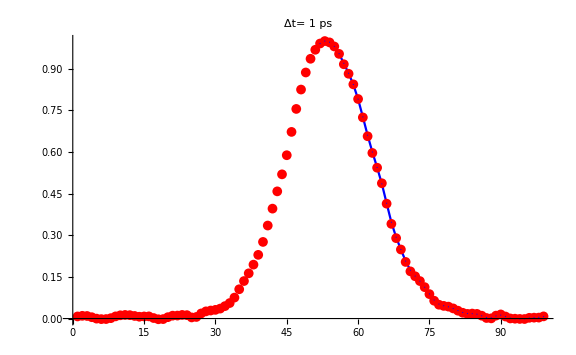
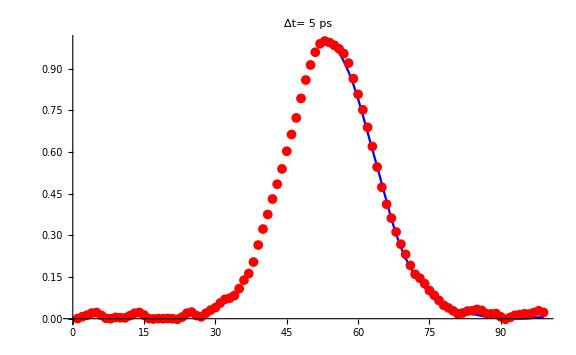
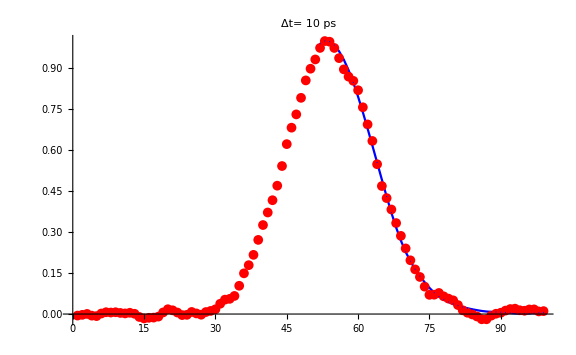
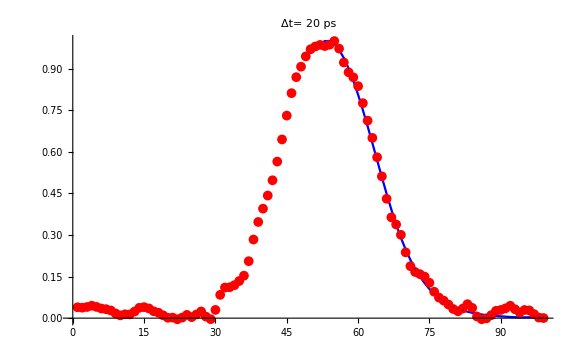
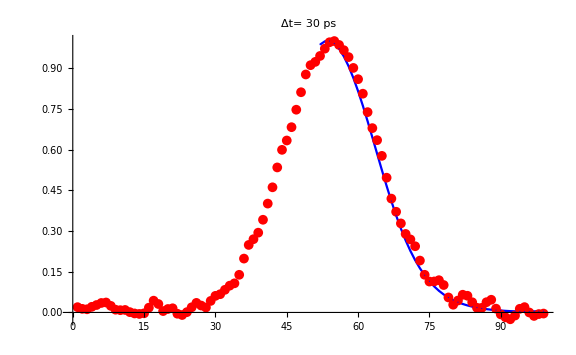
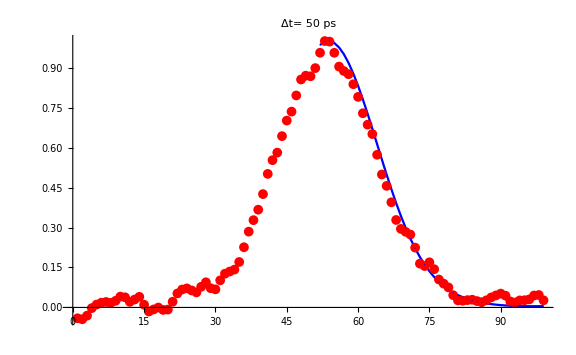

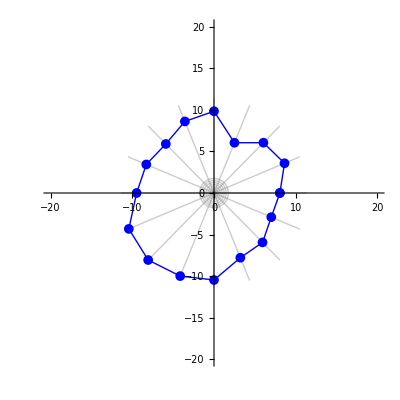

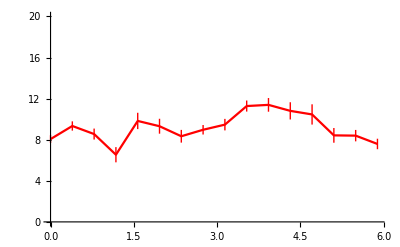

9.22.6

```mathematica
radcomp=4;
Table[ListPlot[{polardat[[j,;;,radcomp]]/Mean[TakeLargest[polardat[[j,;;,radcomp]],1]],Table[{x,nlm2[[radcomp]][timearray[[j]],x]},{x,colcoord,nx2}]},Joined->{False,True},PlotMarkers->{{Automatic, Offset[10]},{Automatic,Offset[1]}},ImageSize->Large,PlotLabel->"Δt= "<>ToString[timearray[[j]]]<>" ps",PlotStyle->{Red,Blue},PlotRange->All],{j,1,Length[timearray]}]
lines={Table[i Pi/(nangles/2),{i,1,First[Dimensions[dcvals]]}],{.25,.5,.75,1.,1.25,1.5,1.75}};
dcvalse=Table[{dcvals[[i,1]],Around[dcvals[[i,2]],2*dcvals[[i,3]]]},{i,First[Dimensions[dcvals]]}];
ListPolarPlot[Catenate[{dcvalse,{dcvalse[[1]]}}],AspectRatio->1,PlotMarkers->{Automatic, Medium}(*,PolarAxes->True*),PlotStyle->{Thick,Blue},PolarGridLines->lines,PlotRange->{{-20,20},{-20,20}},Joined->True]
ListPlot[{dcvalse},PlotRange->{0,20},Joined->True,PlotStyle->Red]
Around[Mean[Table[dcvalse[[i,2]]["Value"],{i,1,nangles}]],Sqrt[Total[Table[(dcvalse[[i,2]]["Uncertainty"])^2,{i,1,nangles}]]]]
```

```mathematica
dcvalse//TableForm
```

0 | 6.00.7
π/8 | 3.80.6
π/4 | 1.70.6
(3 π)/8 | 3.10.9
π/2 | 4.00.9
(5 π)/8 | 3.00.9
(3 π)/4 | 5.00.8
(7 π)/8 | 6.30.8
π | 4.60.8
(9 π)/8 | 6.60.6
(5 π)/4 | 6.90.7
(11 π)/8 | 8.50.8
(3 π)/2 | 11.31.0
(13 π)/8 | 10.70.9
(7 π)/4 | 9.20.9
(15 π)/8 | 8.10.8

```mathematica
t=5;
radcomp=14;
xmin1=Abs[xmax];
xmax1=Abs[xmin];
pixelmat1=Table[x,{x,xmin1,xmax1,(xmax1-xmin1)/(nx2-1)}];
pixelmat2=Table[x,{x,0,2,2/48.}];
```

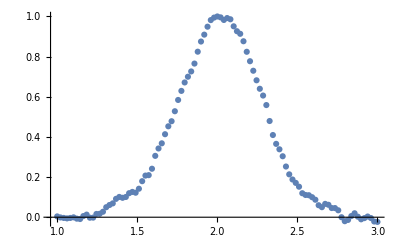

```mathematica
ptab1=polardat[[t,;;,radcomp]]/Mean[TakeLargest[polardat[[t,;;,radcomp]],1]]; 

tab1=Table[{x,nlm2[[radcomp]][timearray[[t]],x]},{x,colcoord,nx2}];
tab1=tab1[[All,2]];

dmat1=Transpose[{pixelmat1,ptab1}];
ListPlot[{dmat1}]
```

```mathematica
SaveDestination="/Users/caseykennedy/Desktop/"; 
Export[SaveDestination<>"B12_13pi_8_t300.txt",dmat1,"TSV"]; (* raw data *)

Export[SaveDestination<>"expteardrop_gaussfit_13pi_8_100ps",Table[{x,nlm2[[3,14]][x]},{x,1,nx2}],"TSV"]  (* fit *)
```